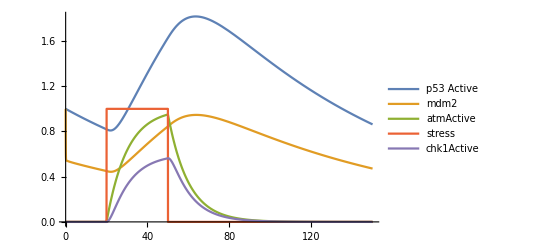

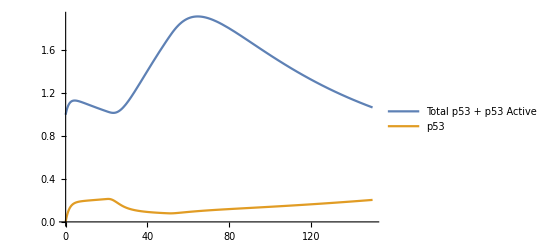

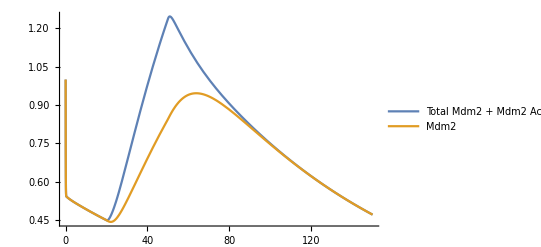

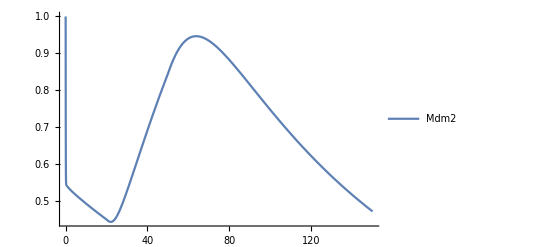

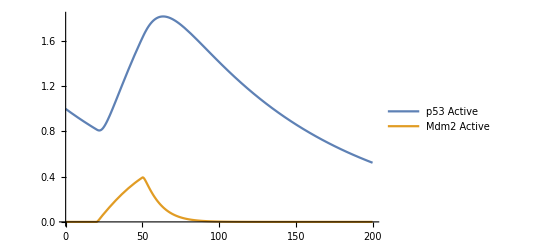

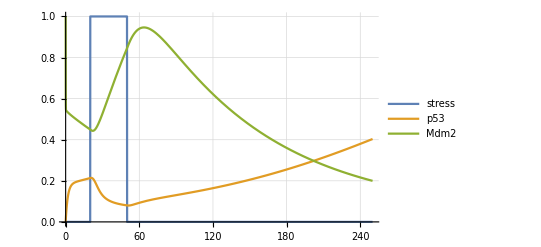

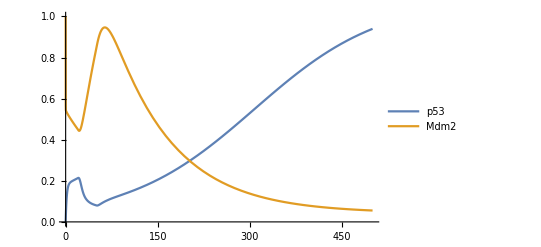

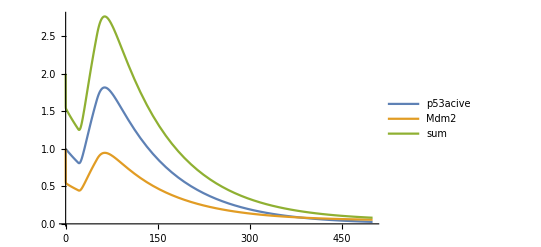

```mathematica
ClearAll["Global`*"]

(*Parameters*)
k1= 0.1;km1 = 0.1; 
k2 = 0.3;km2 = 0.5; 
k3 = 0.1; 
k4 = 1; km4 = 0.01; k4d = 0.0; k4lk = 0.00;
k5 = 0.5*k3;
k6 = 10; k6s = 0.9;
k7= 2*k6; 
k8= 0.5; km8 = 0.5; k8lk = 0.00; k8d =k8;
k9 =  1;
k10 = 0.01; 
k11= 0.02 ;
k12 = 0.01;

(*System Dynamics*)
sol = NDSolve[
{stress[t] ==1(UnitStep[t-20]-UnitStep[t-50]) ,
 
atmActive'[t] ==  k1*stress[t]-km1*atmActive[t], 
(*J1*)

chk1Active'[t] == k2*atmActive[t]- km2*chk1Active[t], 
(*J2*)

p53'[t] == k3-k5*p53[t]-k4*(k4lk+chk1Active[t])*p53[t]+km4*p53Active[t]-k9*mdm2[t]*p53[t], 
(*J3-J4-J5-J9*)

p53Active'[t] == k4*(k4lk+chk1Active[t])*p53[t]-km4*p53Active[t]-k4d*p53Active[t], 
(*J4-J4d*)

mdm2'[t] ==  k6s+k6*p53Active[t]-k7*mdm2[t]-k8*mdm2[t]*(k8lk+atmActive[t])+km8*mdm2Active[t]-k9*p53[t]*mdm2[t], 
(*J6s+J6-J7-J8-J9*)

mdm2Active'[t]== k8*mdm2[t]*(k8lk+atmActive[t])-km8*mdm2Active[t]-k8d*mdm2Active[t], 
(*J8-J8d*)

c0'[t]== k9*p53[t]*mdm2[t]-k10*c0[t]-k11*c0[t], 
(*J9-J10-J11*)

c1'[t]== k11*c0[t]-k12*c1[t], 
(*J11-J12*)


(*stress[0]== atmActive[0]==chk1Active[0]==  0,
stress'[0]== atmActive'[0]==chk1Active'[0]==  0,
c0[0]== .0976, c1[0]== 0.1952,
c0'[ 0]== 0, c1'[ 0]== 0,
mdm2[0]== 2.44375,mdm2'[0]==0,
p53[0]== 0.0401003,p53'[0]== 0,
mdm2Active[0]== 0.0,mdm2Active'[0]== 0.0,
p53Active[0]== 0.0,p53Active'[0]== 0.0},*)
stress[0]== atmActive[0]== chk1Active[0]== c0[0]== c1[0]==0,
mdm2[0]== RandomInteger[],
p53Active[0]== RandomInteger[],
mdm2Active[0]== RandomInteger[],
p53[0]== RandomInteger[]},
{stress,atmActive,chk1Active,p53,p53Active,mdm2, mdm2Active, c0, c1},{t,1500}];

(*Plots*)

Plot[Evaluate[{p53Active[t],mdm2[t],atmActive[t],stress[t], chk1Active[t]}/.sol],{t,0,150},PlotLegends->LineLegend[{"p53 Active", "mdm2", "atmActive", "stress", "chk1Active"}],PlotRange->All]


Plot[Evaluate[{p53[t]+p53Active[t], p53[t]}/.sol],{t,0,150},PlotLegends->LineLegend[{"Total p53 + p53 Active", "p53"}],PlotRange->All]

Plot[Evaluate[{mdm2[t]+mdm2Active[t], mdm2[t]}/.sol],{t,0,150},PlotLegends->LineLegend[{"Total Mdm2 + Mdm2 Active", "Mdm2"}],PlotRange->All]
Plot[Evaluate[{ mdm2[t]}/.sol],{t,0,150},PlotLegends->LineLegend[{ "Mdm2"}],PlotRange->All]
Plot[Evaluate[{p53Active[t],mdm2Active[t]}/.sol],{t,0,200},PlotLegends->LineLegend[{"p53 Active","Mdm2 Active"}],PlotRange->All]

Plot[Evaluate[{stress[t],p53[t],mdm2[t]}/.sol],{t,0,250},PlotLegends->LineLegend[{"stress","p53 ","Mdm2 "}],PlotRange->All,GridLines->Automatic]
Plot[Evaluate[{p53[t],mdm2[t]}/.sol],{t,0,500},PlotLegends->LineLegend[{"p53 ","Mdm2"}],PlotRange->All]

Plot[Evaluate[{p53Active[t],mdm2[t],(p53Active[t]+mdm2[t])}/.sol],{t,0,500},PlotLegends->LineLegend[{"p53acive ","Mdm2","sum "}],PlotRange->All]
Plot[Evaluate[{stress[t],p53Active[t],p53[t]}/.sol],{t,0,500},PlotLegends->LineLegend[{"stress","p53^* ","p53"}],PlotRange->All]

Plot[Evaluate[{stress[t],mdm2Active[t],mdm2[t]}/.sol],{t,0,500},PlotLegends->LineLegend[{"stress","Mdm2^* ","Mdm2"}],PlotRange->All]
```